# The Bipartite Graph Theorem:

I verify the Bipartite graph theorem on a couple of examples

James Pedersen, Jun. 30,  2018

According to theorems 4 and 6 in:

```mathematica
Hyperlink["https://people.orie.cornell.edu/dpw/orie6334/lecture3.pdf"]
```

https://people.orie.cornell.edu/dpw/orie6334/lecture3.pdf

If G is a connected undirected graph G with adjacency matrix A and λ_1≥    ... ≥ λ_n are the eigenvalues of A, G is bipartite iff λ_n=-λ_1. This is the bipartite graph theorem.

## Examples:

Consider the graph

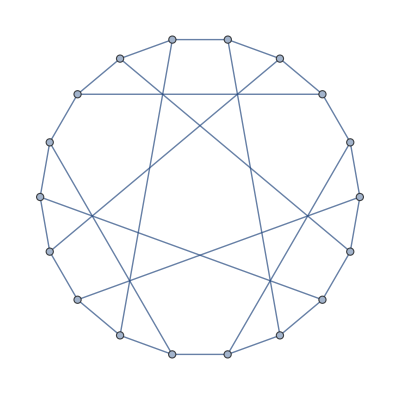

```mathematica
g=GraphData["PappusGraph"]
```

g is a connected graph:

```mathematica
ConnectedGraphQ[g]
```

True

Sorting the eigenvalues of g in ascending order,

```mathematica
Sort[Eigenvalues[AdjacencyMatrix[g]],Less]
```

{-3,-√3,-√3,-√3,-√3,-√3,-√3,0,0,0,0,√3,√3,√3,√3,√3,√3,3}

we see that -(-3) = 3, so g must be bipartite.

```mathematica
BipartiteGraphQ[g]
```

True

In fact, Mathematica’s graph embedding tools make it easy to for one to see that g is bipartite:

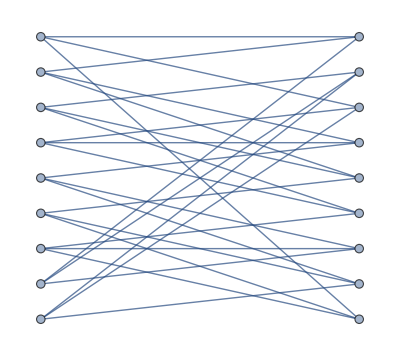

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

What about a negative example? Consider the following graph:

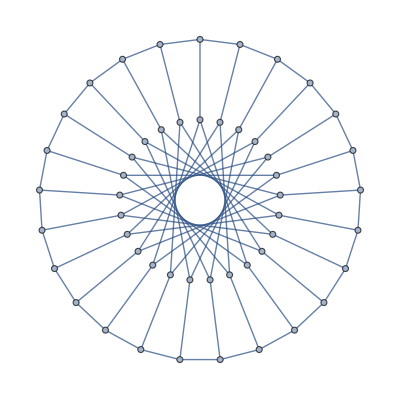

```mathematica
g=PetersenGraph[25,15]
```

```mathematica
Sort[N[Eigenvalues[AdjacencyMatrix[g]]], Less]
```

{-2.74606,-2.74606,-2.46106,-2.46106,-2.32412,-2.32412,-2.07289,-2.07289,-1.94908,-1.94908,-1.88001,-1.88001,-1.87603,-1.87603,-1.3577,-1.3577,-0.994792,-0.994792,-0.731528,-0.731528,-0.431826,-0.431826,-0.0466154,-0.0466154,0.0356204,0.0356204,0.0935099,0.0935099,0.580442,0.580442,0.957921,0.957921,1.,1.12418,1.12418,1.23806,1.23806,1.4027,1.4027,2.12259,2.12259,2.19914,2.19914,2.258,2.258,2.33503,2.33503,2.52452,2.52452,3.}

Here -2.74606 is not equal to -3, so g cannot be bipartite.

```mathematica
BipartiteGraphQ[g]
```

False

Note that attempting to visualize g as a bipartite graph fails, as expected:

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

One more large example, creating a large undirected graph directly from a random 50x50 adjacency matrix:

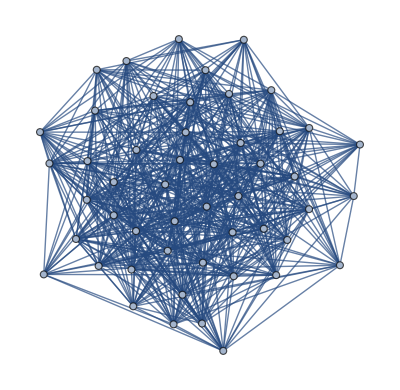

```mathematica
B=50;
A=Table[Table[If[k<l,RandomInteger[1],0],{l,1,B}],{k,1,B}];
B=Transpose[A];
adjmatrix=A+B;
Dimensions[adjmatrix];
SymmetricMatrixQ[adjmatrix];
g=UndirectedGraph[AdjacencyGraph[adjmatrix]]
```

Odds are that g will be connected yet not bipartite:

```mathematica
ConnectedGraphQ[g]
BipartiteGraphQ[g]
list=N[Sort[Eigenvalues[adjmatrix],Less]]
```

True

False

{-7.13749,-6.23377,-5.69327,-5.48302,-5.25683,-4.90149,-4.8475,-4.51198,-4.15107,-3.85244,-3.67306,-3.38214,-3.29365,-3.08944,-2.91825,-2.81661,-2.49561,-2.28344,-2.00102,-1.56365,-1.44728,-1.34024,-1.23216,-0.84555,-0.399136,-0.225044,-0.0583955,0.150549,0.246833,0.595835,0.790193,0.872142,0.958683,1.50826,1.66746,2.06423,2.22938,2.28126,2.65021,3.0903,3.44125,3.51978,3.66745,3.96047,4.39964,5.05651,5.20615,5.63461,5.89507,25.2473}